#### In this notebook, we calculate the dynamics of the wave front with a Heaviside activation function; we explicitly plot the concentration profiles from figures 1 and 2 and the concentration gradients a la figure 4 of Dieterle et al. (2020).

First, we define the system parameters; vBase is the desired wave speed, Dc is the diffusion constant, cellDim is the number of dimensions in which the cells live, diffDim is the number of dimensions in which diffusion takes place, Cth is the threshold concentration (implicitly normalized by the emission rate, a, and cell density, rho) which gives the desired wave speed vBase given the other system parameters, and rInv is the initial signaling radius.

```mathematica
vBase = 2. 10^-6;
Dc=  1. 10^-10;

cellDim = 2;
diffDim = 2;

(*If diffDim == cellDim, this gives Cth = Dc/vBase^2; if diffDim == cellDim+1, it gives Cth = 2/Pi/vBase*)
Cth = (diffDim+1-cellDim)Dc/vBase^2+(diffDim-cellDim)2/(Pi vBase);

rInv =3 Dc/vBase;
```

Next, we write down the Green's function for each dimensionality; this calculation assumes a spherically symmetric environment. The Green's function describes the concentration generated at radius r by a spherical (circular ring for sources in 2D, point for sources in 1D) shell at radius R; the shell is assumed to have made a momentary emission at time tt and the concentration is measured at a later time t = tt+T. The diffusion constant is Dc. GF is the desired Green’s function given diffDim and cellDim. gradGF is the radial gradient of these functions

```mathematica
GF11[r_,R_, T_] :=1/Sqrt[4 Pi Dc T] Exp[-(r-R)^2/(4 Dc T)];
GF12[r_,R_, T_] := 1/(2 Pi Dc T)Exp[-(r-R)^2/(4 Dc T)];
GF22[r_,R_, T_] := R/(2Dc T)Exp[-(r^2+R^2)/(4 Dc T)]BesselI[0,(r R)/(2 Dc T)];
GF23[r_,R_, T_] := R/(Sqrt[4Pi] (Dc T)^(3/2))Exp[-(r^2+R^2)/(4 Dc T)]BesselI[0,(r R)/(2 Dc T)];
GF33[r_,R_, T_] := R/(r Sqrt[Pi Dc T])Sinh[(r R)/(2 Dc T)]Exp[-(r^2+R^2)/(4 Dc T)];

GF[r_,R_, T_]:=ToExpression["GF"<>ToString[cellDim]<>ToString[diffDim]][r,R, T];



gradGF11[r_,R_, T_] :=(R-r)/(4 √π (Dc T)^(3/2))ⅇ^(-(r-R)^2/(4 Dc T)) ;
gradGF12[r_,R_, T_] := (R-r)/(4 Dc^2 π  T^2)ⅇ^(-(r-R)^2/(4 Dc T)) ;
gradGF22[r_,R_, T_] := R/(4 Dc^2  T^2)ⅇ^(-(r^2+R^2)/(4 Dc T)) (R BesselI[1,(r R)/(2 Dc T)]-r BesselI[0,(r R)/(2 Dc T)]);
gradGF23[r_,R_, T_] := R/(4 √π (Dc T)^(5/2))ⅇ^(-(r^2+R^2)/(4 Dc T))(R BesselI[1,(r R)/(2 Dc T)]-r BesselI[0,(r R)/(2 Dc T)]);
gradGF33[r_,R_, T_] := (R^2/r)/(2 √π(Dc T)^(3/2))ⅇ^(-(r^2+R^2)/(4 Dc T))(Cosh[(r R)/(2 Dc T)]-(r^2+2 Dc T)/(r R)Sinh[(r R)/(2 Dc T)]);

gradGF[r_,R_, T_]:=ToExpression["gradGF"<>ToString[cellDim]<>ToString[diffDim]][r,R, T];
```

Since our goal is to calculate the wave front dynamics in our system, we must compute the concentration profile as it evolves in time. For Heaviside activation, computing the wave front position will directly allow for the computation of the concentration profile, since the latter involves an integral of the Green’s function against the former. To start, we define the numerical precision and desired duration of this computation.

```mathematica
(*Duration of the computation; this should ideally be many multiples of the characteristic time, Dc/vBase^2*)
tMax =10 Dc/vBase^2;
(*Time step of the computation; this should ideally be a small fraction of the characteristic time, Dc/vBase^2*)
Δt = Dc/vBase^2/5;
Print["Number of simulation steps: "<>ToString[tMax/Δt]]

(*Spatial precision of the wave front finder; this should be a small fraction of the distance travelled by the wave front in one time step*)
δr = vBase Δt/100;
(*Define a maximum step size of the wave front finder; this needs only to be a few multiples of the distance travelled by the wave front in one time step*)
Δr = N[2vBase Δt];
(*Define the number of steps needed to achieve a maximum step size of Δr and a precision of δr*)
searchNum = Ceiling[Log2[Δr/δr]];
(*Define the step sizes*)
rSteps = Table[Δr/2^i,{i,1,searchNum}];

(*How many time steps do you want to take before the solver updates its progress?*)
updateNum = 10;
```

Number of simulation steps: 50.

Next, we calculate the initiation time of the wave by finding the time at which the concentration at rInv exceeds Cth. To do so, we step halfway to tMax and check if the concentration exceeds Cth. If it does, we step a quarter way; if it doesn’t we step three quarters of the way. Repeatedly dividing the time interval in half, we eventually converge to the initiation time tInit up to a precision of Δt. In our numerical integration, we use the LocalAdaptive option to handle the singularity around T=0. Thusly, we have defined a function, initTime, which takes as arguments rInv, tMax, and Δt.

```mathematica
(*How many time steps are needed to divide the interval of length tMax to resolution Δt?*)
nTimeSteps = Ceiling[Log2[tMax/Δt]];
(*Calculate the time steps*)
timeSteps = Table[tMax/2^i,{i,1,nTimeSteps}];
(*An array that keeps track of how far to walk*)
timeBools = Table[1,{i,1,nTimeSteps}];

recMax = 15;
nIntOp = {"LocalAdaptive","MaxRecursion"->recMax};

initTime[rInv_,tMax_,Δt_]:=Do[
numSteps = Ceiling[Log2[tMax/Δt]];
tSteps = Table[tMax/2^i,{i,1,numSteps}];
tBools = Table[1,{i,1,numSteps}];
For[i=1,i<numSteps+1,i++,
test = Δt Ceiling[1/Δt Total[(tSteps tBools)[[1;;i]]]];
cTest = NIntegrate[GF[rInv,R,tt],{R,-rInv+rInv HeavisideTheta[cellDim-1.5],rInv},{tt,0,test},Method->nIntOp];
If[cTest>Cth,tBools[[i]]=0];
If[i==numSteps,Return[Δt Ceiling[1/Δt Total[tSteps tBools[[1;;i]]]]]]
];,
{n,1}];

tInit = initTime[rInv, tMax, Δt]
```

60.

We then compute the location of the wave front at every subsequent time point up to tMax. To do so, we keep track of the wave front location and construct a linear interpolation of the wave front position, then integrate this against the Green’s function.

```mathematica
(*An array that keeps track of the wave front location*)
nSteps = Ceiling[(tMax-tInit)/Δt];
rCrit = ConstantArray[{0,0},nSteps+2];
rCrit[[1]] = {0,rInv};
rCrit[[2]]={tInit,rInv};

(*Compute the wave front locations in time*)
For[i=1,i<nSteps+1,i++,
t = tInit+i Δt;

rStart = rCrit[[i+1,2]];
rBools = Table[1,{i,1,searchNum}];

For[j = 1,j<searchNum+1,j++,
rTest = rStart+Total[(rBools rSteps)[[1;;j]]];

fTest = Interpolation[Append[rCrit[[1;;i+1]],{t,rTest}],InterpolationOrder->1];
concTest = NIntegrate[GF[rTest,R,t-tt],{tt,0,t},{R,0,fTest[tt]},Method->nIntOp];

If[concTest<Cth,rBools[[j]]=0];
If[j==searchNum,rCrit[[i+2]]={t,rStart+Total[(rBools rSteps)[[1;;j]]]}];
];
If[Mod[i,updateNum]==0,Print[ToString[100.i/nSteps]<>"% complete"]]
]
```

26.3158% complete

52.6316% complete

78.9474% complete

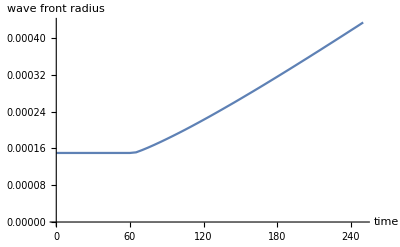

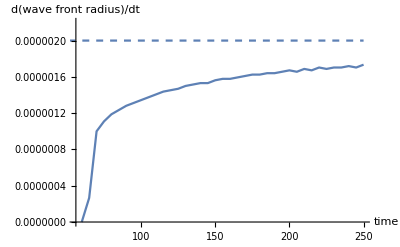

```mathematica
(*Plot the wave front radius in time*)
ListPlot[rCrit,Joined->True, AxesLabel->{"time", "wave front radius"}]

(*Also plot the rate of change of the wave front location*)
wfTimes = Transpose[rCrit][[1]];
wfRad = Transpose[rCrit][[2]];
wfSpeeds = (wfRad[[2;;]]-Drop[wfRad,-1])/Δt;

Show[ListPlot[Transpose[{wfTimes[[2;;]],wfSpeeds}],Joined->True, AxesLabel->{"time", "d(wave front radius)/dt"},PlotRange->{0,1.1vBase}],
Plot[vBase,{t,0,Last[wfTimes]},PlotStyle->Dashed]]
```

Next, we wish to visualize the concentration profile at the end of our numerical simulation, so we look at it from r = 0 to 1.5 times the largest wave front radius achieved.

```mathematica
(*Number of points at which to evaluate the concentration*)
nConcPts = 50;

(*Maximum radius to observe*)
rMax = 1.5Last[rCrit][[2]];
(*Radii at which to calculate the concentration profile*)
rPts = Subdivide[rInv,rMax,nConcPts];

(*Time at which we wish to observe the concentration*)
tEval = Last[rCrit][[1]];

(*Calculate the concentration using the previously attained wave front locations*)
interpFunc = Interpolation[rCrit,InterpolationOrder->1];
conc = NIntegrate[GF[rPts,R,tEval-tt],{tt,0,tEval},{R,0,interpFunc[tt]},Method->nIntOp];
```

Next, we calculate the concentration profile according to our asymptotic theory. This varies depending on system dimensionality -- i.e., whether cellDim = diffDim -- which we take into account below.

```mathematica
(*First, turn rPts into a distance from the wave front*)
rTilde = rPts-Last[rCrit][[2]];

(*Then, calculate the concentration according to the system dimensionality.*)
concTheory = If[cellDim==diffDim,
Cth HeavisideTheta[rTilde]Exp[-rTilde/(Dc/vBase)]+(Cth-rTilde/vBase)HeavisideTheta[-rTilde],
1/(Pi vBase)(HeavisideTheta[rTilde]NIntegrate[(1-1/Sqrt[1+k^2])/k^2 Exp[-(vBase rTilde)/(2 Dc)(Sqrt[k^2+1]+1)],{k,-Infinity,Infinity}]+HeavisideTheta[-rTilde]NIntegrate[2/k^2-(1+1/Sqrt[1+k^2])/k^2 Exp[(vBase rTilde)/(2 Dc)(Sqrt[k^2+1]-1)],{k,-Infinity,Infinity}])];
```

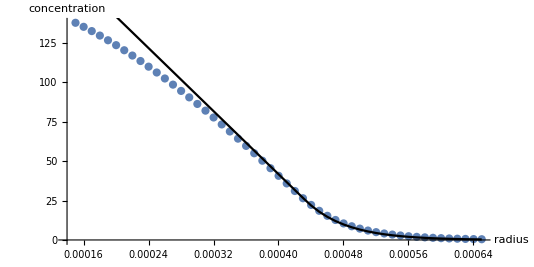

```mathematica
(*Plot!!!*)
Show[ListPlot[Transpose[{rPts,conc}],AxesLabel->{"radius","concentration"}],
ListPlot[Transpose[{rPts,concTheory}],Joined->True,PlotStyle->Black],
AspectRatio->1/2]
```

We compute radial gradients of the asymptotic concentration profiles a la figure 4 in a similar manner to the above analysis. We may compare this to the gradients generated by a static disk (of radius rInv) of cells -- the “simple diffusion” model -- by numerical integration of said source.

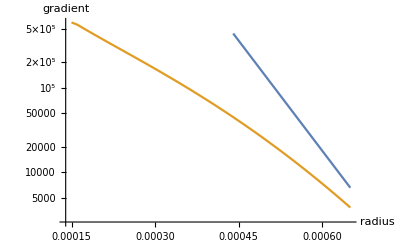

```mathematica
gradRelayTheory = If[cellDim==diffDim,
vBase Cth HeavisideTheta[rTilde]Exp[-rTilde/(Dc/vBase)]/Dc-HeavisideTheta[-rTilde]/vBase,
1/(2Pi Dc)(HeavisideTheta[rTilde]NIntegrate[1/Sqrt[k^2+1] Exp[-(vBase rTilde)/(2 Dc)(Sqrt[k^2+1]+1)],{k,-Infinity,Infinity}]+HeavisideTheta[-rTilde]NIntegrate[1/Sqrt[1+k^2] Exp[(vBase rTilde)/(2 Dc)(Sqrt[k^2+1]-1)],{k,-Infinity,Infinity}])];


gradSimpleDiff = -NIntegrate[gradGF[rPts,R,tEval-tt],{R,0,rInv},{tt,0,tEval},Method->nIntOp];



ListLogPlot[{Transpose[{rPts,gradRelayTheory}],Transpose[{rPts,gradSimpleDiff}]},Joined->True,AxesLabel->{"radius","gradient"}]
```

Finally, we compute the initiation time for a range of rInv defined by [rInvMin, rInvMax] with nrInv total values. We plot the asymptotic forms of the initiation times alongside the numerically calculated forms. In this section of code, we assume that cellDim = diffDim for purposes of calculating the theoretical initiation time.

```mathematica
(*The minimum initiating colony sizes for 1, 2, and 3 dimensions*)
rInvMin = {0.1Dc/vBase,0.6 Dc/vBase,Sqrt[3]Dc/vBase};
rInvMax = 10 Dc/vBase;
nrInv = 25;

(*maximum time considered in the numerics*)
maxInitTime = 20000 Dc/vBase^2;
(*numerical time resolution*)
initTimeRes = 0.01 Dc/vBase^2;

(*construct an array with all the desired rInv values*)
rInvVals = rInvMin[[diffDim]] Table[(rInvMax/rInvMin[[cellDim]])^((i-1)/(nrInv-1)),{i,1,nrInv}];

(*compute the initiation times*)
inits = Table[initTime[rInvVals[[i]],maxInitTime,initTimeRes],{i,1,Length[rInvVals]}];
```

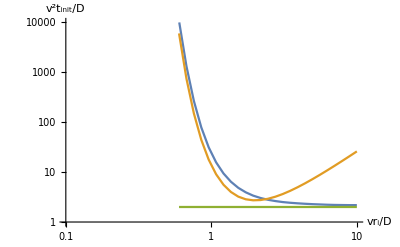

```mathematica
(*calculate the theoretical initiation times (normalized by Dc/vBase^2) at small rInv*)
theoryInitSmall = vBase^2/Dc{(Cth Sqrt[Pi Dc]/2/rInvVals)^2,(rInvVals^2/(4 Dc))Exp[((2Dc)/(vBase rInvVals))^2],(rInvVals(1-(3 Cth Dc)/rInvVals^2)^-1)^2/Pi Dc};

(*plot away!*)
ListLogLogPlot[{Transpose[{vBase rInvVals/Dc,vBase^2 inits/Dc}],Transpose[{vBase rInvVals/Dc,theoryInitSmall[[diffDim]]}],Transpose[{vBase rInvVals/Dc,0.rInvVals+2.}]},PlotRange->{{0.1,10},{1,vBase^2 maxInitTime/Dc/2}},AxesLabel->{"vr_i/D","v^2t_init/D"},Joined->True]
```